Depth and diameter calcs:

```mathematica
hdratio=Sqrt[2/3]/(2 nrings+1);
Solve[h==Sqrt[2/3]*L,L]
Solve[d==Sqrt[2/3]*L/hdratio,nrings]
```

{{L→√(3/2) h}}

{{nrings→(d-L)/(2 L)}}

```mathematica
Sqrt[3/2.]*7
```

8.57321

```mathematica
3*8.573214099741122
```

25.7196

Matlab code calcs:

```mathematica
Solve[(L/2)^2+x^2==(Sqrt[3]/2*L-x)^2,x]
```

{{x→L/(2 √3)}}

```mathematica
Simplify[Sqrt[((L*Sqrt[3])/6)^2+(L/2+n*L)^2]]
```

√(L^2/12+(L/2+L n)^2)

```mathematica
Simplify[√(L^2/12+L^2(1/2+n)^2)]
```

√(L^2/12+L^2 (1/2+n)^2)

```mathematica
r[n_]:=L*√(1/12+(1/2+n)^2)
```

```mathematica
r[0]
```

L/(√3)

```mathematica
Simplify[Sqrt[3]/2*L-L/(2 √3)]
```

L/(√3)

```mathematica
Simplify[(L/2+n*L)/(L*Sqrt[3]/6)]
```

√3 (1+2 n)

```mathematica
θ[n_]:=ArcTan[√3 (1+2 n)]-π/3
```

```mathematica
θ[0]
```

0

```mathematica
θ[1]*180./π
```

19.1066

```mathematica
θ[2]*180./π
```

23.4132

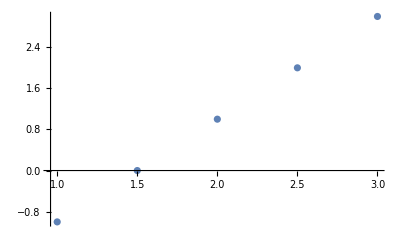

```mathematica
P1={1,-1};
P2 = {3,3};
P3 = 2/3*P1+1/3*P2;
P4=1/3*P1+2/3*P2;
P5 =3/4*P1+1/4*P2;
P6=2/4*P1+2/4*P2;
P7=1/4*P1+3/4*P2;
ListPlot[{P1,P2,P5,P6,P7}]
```